```mathematica
SetDirectory["~/GitHub/DIO_point_spec"]
```

/Users/robert/GitHub/DIO_point_spec

```mathematica
j0=Import["Zal0.1_j0.dat"];
j1k1=Import["test_Zal.1_j1_k-1.dat"]
j1k2=Import["test_Zal.1_j1_k-2.dat"]
j2k1=Import["test_Zal.1_j2_k-2.dat"]
j2k2=Import["test_Zal.1_j2_k-3.dat"]
```

{{0.00001,3.13427×10^-9},{0.10001,0.0931203},{0.20001,0.111946},{0.30001,0.0943267},{0.40001,0.0659276},{0.50001,0.0150824},{0.60001,0.0000565009},{0.70001,1.23902×10^-6},{0.80001,3.15771×10^-8},{0.90001,2.48844×10^-10}}

{{0.00001,6.46096×10^-18},{0.10001,0.0183476},{0.20001,0.0550638},{0.30001,0.0720549},{0.40001,0.0744733},{0.50001,0.0267117},{0.60001,0.0000920236},{0.70001,1.69997×10^-6},{0.80001,4.22104×10^-8},{0.90001,3.89641×10^-10}}

{{0.00001,3.17981×10^-17},{0.10001,0.0514642},{0.20001,0.113174},{0.30001,0.119403},{0.40001,0.0967982},{0.50001,0.0265476},{0.60001,0.0000692039},{0.70001,7.59284×10^-7},{0.80001,7.85363×10^-9},{0.90001,1.4754×10^-11}}

{{0.00001,7.18781×10^-26},{0.10001,0.00989677},{0.20001,0.0527265},{0.30001,0.0830107},{0.40001,0.0923204},{0.50001,0.0346593},{0.60001,0.0000716549},{0.70001,5.84559×10^-7},{0.80001,4.97843×10^-9},{0.90001,8.58715×10^-12}}

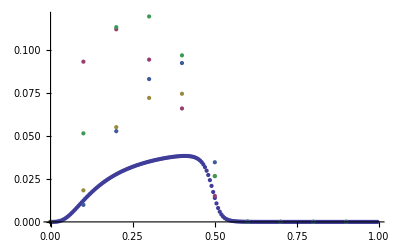

```mathematica
ListPlot[{j0,j1k1,j1k2,j2k1,j2k2}]
```

```mathematica
S1=Table[{j0[[k,1]],j0[[k,2]]+j1k1[[k,2]]+j1k2[[k,2]]},{k,1,Length[j0]}]
```

{{0.00001,3.13995×10^-9},{0.10001,0.123853},{0.20001,0.194707},{0.30001,0.201437},{0.40001,0.178697},{0.50001,0.0556996},{0.60001,0.000207806},{0.70001,4.50147×10^-6},{0.80001,1.2398×10^-7},{0.90001,1.16553×10^-9}}

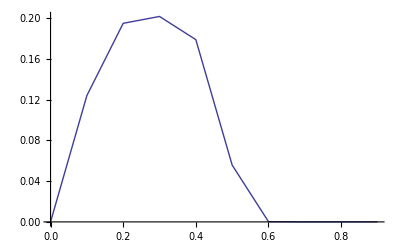

```mathematica
ListPlot[S1,Joined->True]
```

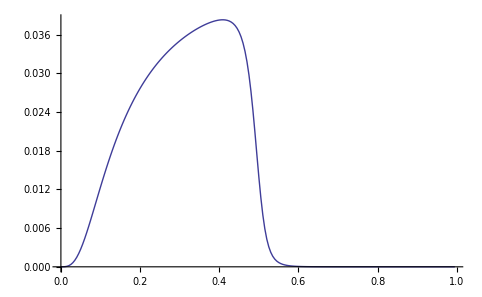

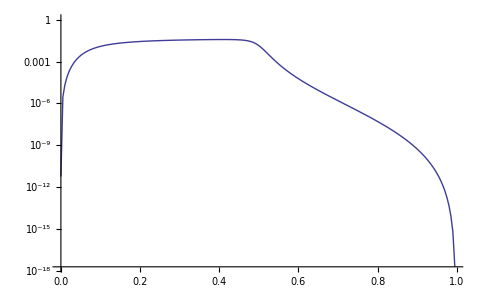

```mathematica
ListPlot[j0, Joined->True]
ListLogPlot[j0, Joined->True]
```